1/50000000

10 π

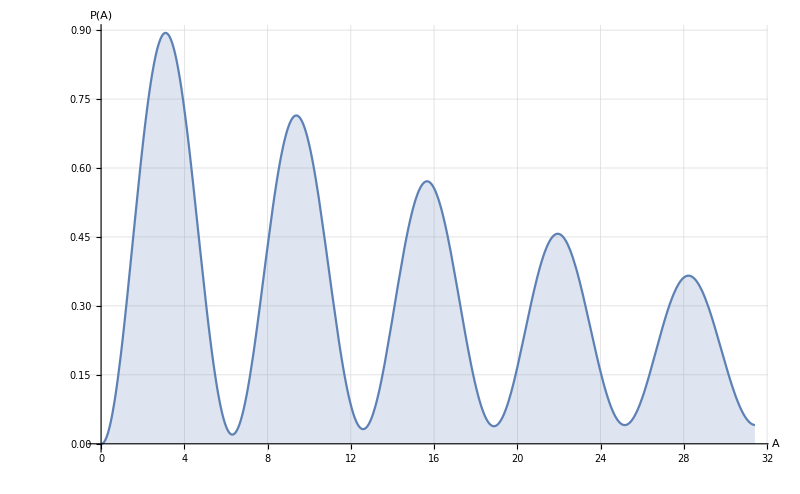

```mathematica
ns = 10^-9;
MHz = 10^6;
Subscript[γ, 10] = 0;
Γ0 =  0;
η = 0;
Γ = 1/2(Γ1 + Subscript[γ, ϕ]);
P[A_] :=  1/2*(Exp[- 1/2 Γ1 * A/Ω]+ Exp[-1/4(2Γ + Γ1 ) * A/Ω]*Sin[A + Θ]);

τmax = 20 ns
pulseArea = 10π
varParams = {Θ -> -1.6, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(20 ns), Ω -> pulseArea/τmax };
plt1 = Plot[{{P[A] /. varParams}}, {A,0,pulseArea}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"A", "P(A)"}]
```

```mathematica
Pnorm1 = Integrate[P[A],{A, 0, ∞}];
P2a =Integrate[P[a]*P[A - a], {a, 0, A}];
Pnorm2 = Pnorm1^2;
P2at[A_] =P2a;
P3a =Integrate[P2at[a]*P[A - a], {a, 0, A}];
Pnorm3 = Pnorm1^3;
P3at[A_] =P3a;
```

1/1000000000

6 π

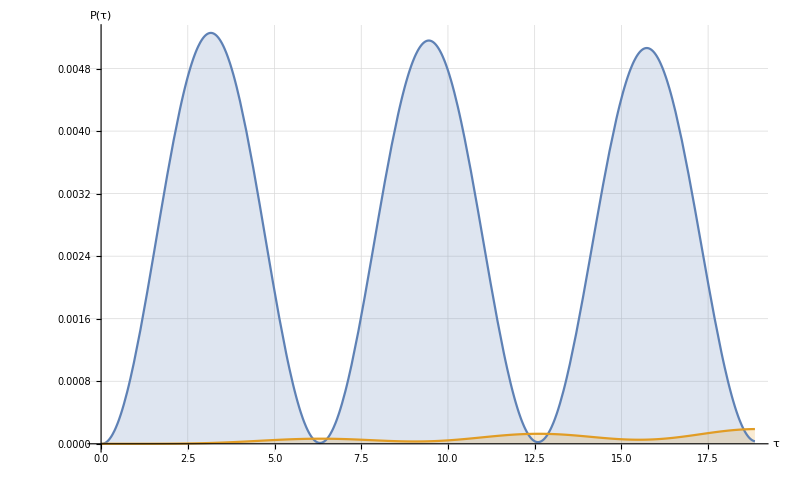

```mathematica
τmax = 1ns
pulseArea = 6π
varParams = {Θ -> -1.6, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(20 ns), Ω -> pulseArea/τmax };
plt1 = Plot[{{P[A]/Pnorm1 /. varParams},  {P2at[A]/Pnorm2 /. varParams}}, {A,0,pulseArea}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"τ", "P(τ)"}]
```

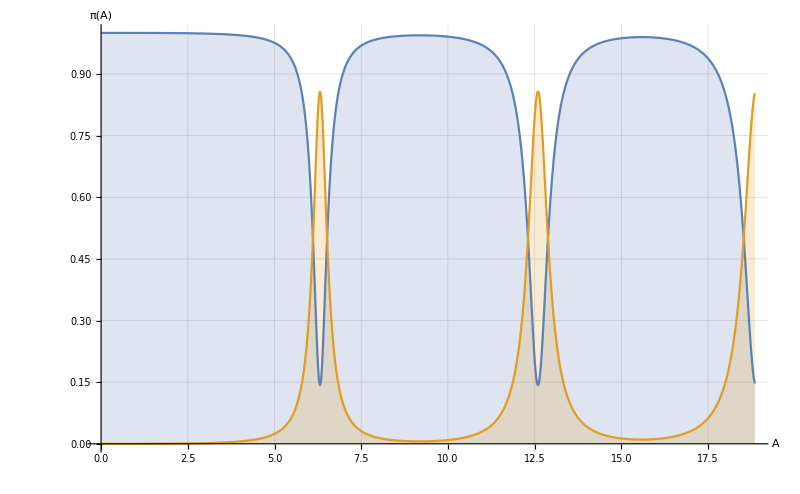

```mathematica
plt1 = Plot[{{P[A]/(Pnorm1(P[A]/Pnorm1 +P2at[A]/Pnorm2)) /. varParams},  {P2at[A]/(Pnorm2(P[A]/Pnorm1 +P2at[A]/Pnorm2)) /. varParams}}, {A,0,pulseArea}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"A", "π(A)"}]
```

6 π

1.×10^-10

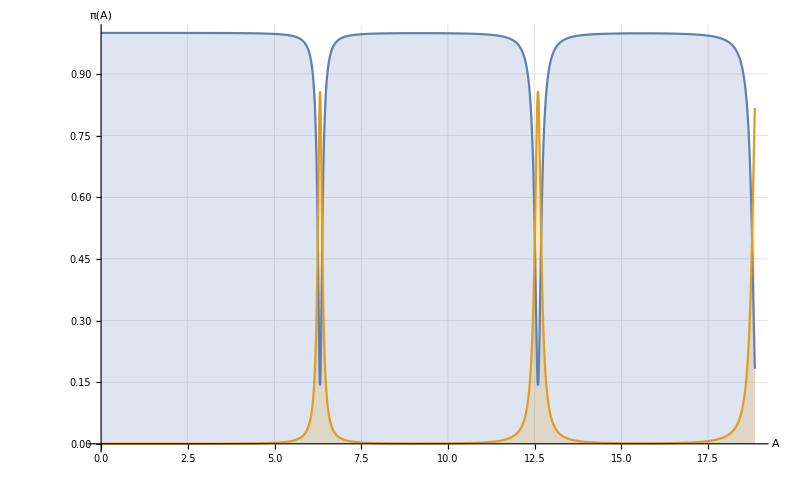

```mathematica
pulseArea = 6π
τmax = 0.1 ns
varParams = {Θ -> -1.6, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(20 ns), Ω -> pulseArea/τmax };
plt1 = Plot[{{P[A]/(Pnorm1(P[A]/Pnorm1 +P2at[A]/Pnorm2)) /. varParams},  {P2at[A]/(Pnorm2(P[A]/Pnorm1 +P2at[A]/Pnorm2)) /. varParams}}, {A,0,pulseArea}, PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, Filling->0,LabelStyle->(FontSize->25), PlotStyle -> Automatic, AxesLabel->{"A", "π(A)"}]
```

6 π

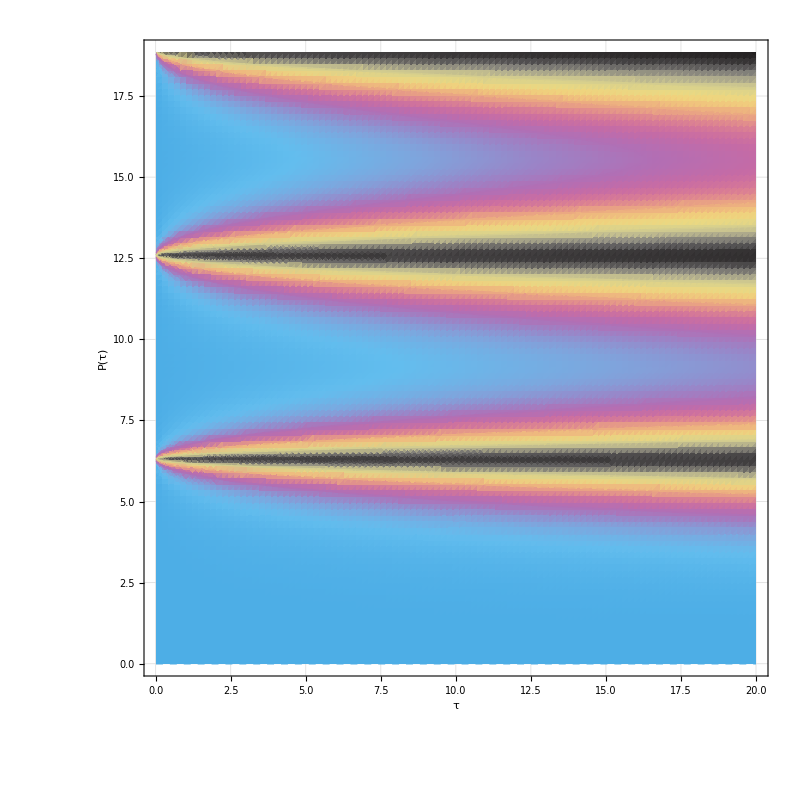

```mathematica
pulseArea = 6π
plt1 = DensityPlot[{P2at[A]/(Pnorm2(P[A]/Pnorm1 +P2at[A]/Pnorm2)) /. {Θ -> -1.6, Γ1 -> 1/(10 ns), Subscript[γ, ϕ] -> 1/(10 ns), Ω -> pulseArea/(τmax ns) }}, {τmax, 0.01, 20}, {A,0,pulseArea},PlotRange-> All,GridLines-> Automatic,ImageSize-> 800,PlotPoints->100, LabelStyle->(FontSize->25),ColorFunction->"CMYKColors",PlotPoints->35,MeshFunctions->{#3&,#3&},Mesh->{Range[-1,1,0.4],Range[-0.8,0.8,0.4]},MeshStyle->{Black,Dashed},Axes->True, AxesLabel->{"τ", "P(τ)"}]
```